```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=4;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=15*κ;
min1=-15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{{-15.,1.698},{-14.,2.48561},{-13.,1.63933},{-12.,0.920898},{-11.,0.44302},{-10.,0.0606912},{-9.,-0.277478},{-8.,-0.596709},{-7.,-0.913103},{-6.,-1.23974},{-5.,-1.58985},{-4.,-1.97925},{-3.,-2.42895},{-2.,-2.96726},{-1.,-3.61977},{0.,-4.12808},{1.,-3.61977},{2.,-2.96726},{3.,-2.42895},{4.,-1.97925},{5.,-1.58985},{6.,-1.23974},{7.,-0.913103},{8.,-0.596709},{9.,-0.277478},{10.,0.0606912},{11.,0.44302},{12.,0.920898},{13.,1.63933},{14.,2.48561},{15.,1.698}}

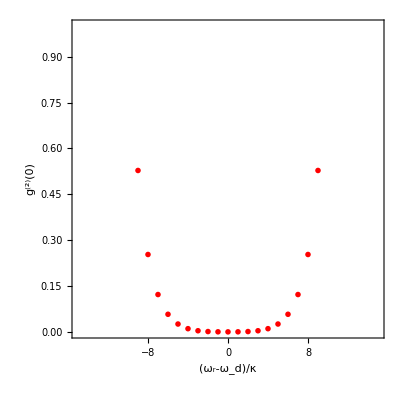

```mathematica
data={{-15.,1.6979955845880512},{-14.,2.4856122954968907},{-13.,1.6393333619548986},{-11.999999999999998,0.920897678966617},{-10.999999999999998,0.44301960622939024},{-10.,0.06069120160452289},{-8.999999999999998,-0.2774779408689168},{-7.999999999999999,-0.5967093805851598},{-7.,-0.9131030116086176},{-6.,-1.239744264738045},{-5.,-1.589853880522737},{-4.,-1.97925268523589},{-2.9999999999999987,-2.42895310711525},{-1.9999999999999991,-2.967261386359606},{-0.9999999999999996,-3.6197705920588232},{0.,-4.128078311678063},{0.9999999999999996,-3.6197705920588232},{1.9999999999999991,-2.967261386359606},{2.9999999999999987,-2.42895310711525},{3.9999999999999982,-1.9792526852358912},{5.,-1.589853880522737},{5.999999999999999,-1.2397442647380452},{6.999999999999999,-0.9131030116086176},{8.000000000000002,-0.5967093805851584},{9.000000000000002,-0.27747794086891514},{10.000000000000002,0.06069120160452365},{11.000000000000002,0.4430196062293909},{12.,0.9208976789666179},{13.,1.6393333619548986},{14.,2.4856122954968907},{15.,1.6979955845880512}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Red},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=16;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=23;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f;
Jrf=σr1f+σr2f+σr3f+σr4f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,1}]];
{m,logg20},{m,-15,15,1}];

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

{{-15,1.20776},{-14,0.796594},{-13,1.00661},{-12,0.745973},{-11,0.383232},{-10,0.037429},{-9,-0.273742},{-8,-0.592653},{-7,-0.885391},{-6,-1.22131},{-5,-1.54782},{-4,-1.92887},{-3,-2.38088},{-2,-2.79585},{-1,-3.38557},{0,-3.54472},{1,-3.27208},{2,-2.87925},{3,-2.33816},{4,-1.93725},{5,-1.55708},{6,-1.20459},{7,-0.904365},{8,-0.575408},{9,-0.280408},{10,0.0422605},{11,0.386141},{12,0.748012},{13,1.00602},{14,0.797421},{15,1.206}}

```mathematica
data={{-15,1.2077585462407605},{-14,0.7965943791430202},{-13,1.0066106188536599},{-12,0.7459732298406575},{-11,0.38323168499159654},{-10,0.0374289593059373},{-9,-0.2737418927568862},{-8,-0.592653050303169},{-7,-0.8853905534696785},{-6,-1.2213146475904175},{-5,-1.5478178864746222},{-4,-1.928867169081583},{-3,-2.380875443424697},{-2,-2.7958527010179988},{-1,-3.385567353885887},{0,-3.54471649699318},{1,-3.272076929982168},{2,-2.87925186800203},{3,-2.3381565133873368},{4,-1.9372479628862507},{5,-1.55708125740216},{6,-1.2045860549751863},{7,-0.90436475915716},{8,-0.5754075656921134},{9,-0.28040822942550886},{10,0.042260487075873626},{11,0.3861406513465099},{12,0.7480123337275035},{13,1.0060213500180593},{14,0.7974207031563332},{15,1.2060037891011637}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Red},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

-Graphics-

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=5;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=15*κ;
min1=-15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{{-15.,2.07338},{-14.,1.22332},{-13.,0.709097},{-12.,0.32109},{-11.,-0.00773381},{-10.,-0.306714},{-9.,-0.592305},{-8.,-0.875864},{-7.,-1.16693},{-6.,-1.47509},{-5.,-1.81155},{-4.,-2.1909},{-3.,-2.63337},{-2.,-3.16671},{-1.,-3.81596},{0.,-4.32218},{1.,-3.81596},{2.,-3.16671},{3.,-2.63337},{4.,-2.1909},{5.,-1.81155},{6.,-1.47509},{7.,-1.16693},{8.,-0.875864},{9.,-0.592305},{10.,-0.306714},{11.,-0.00773381},{12.,0.32109},{13.,0.709097},{14.,1.22332},{15.,2.07338}}

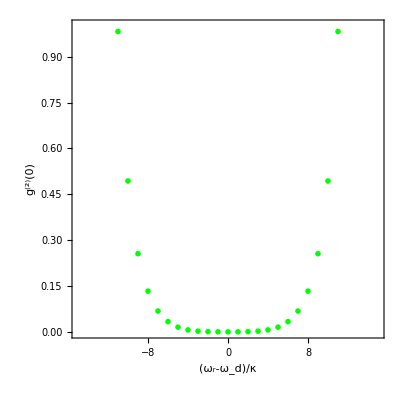

```mathematica
data={{-15.,2.073378761994495},{-14.,1.2233159168465897},{-13.,0.7090974225790078},{-11.999999999999998,0.3210895516356274},{-10.999999999999998,-0.007733808413306255},{-10.,-0.3067141537773974},{-8.999999999999998,-0.5923053367541407},{-7.999999999999999,-0.8758640968734112},{-7.,-1.1669267021348635},{-6.,-1.4750862197840962},{-5.,-1.8115477889315905},{-4.,-2.190899632886562},{-2.9999999999999987,-2.633365513150825},{-1.9999999999999991,-3.1667065513094577},{-0.9999999999999996,-3.815956399183764},{0.,-4.322179401407325},{0.9999999999999996,-3.815956399183764},{1.9999999999999991,-3.1667065513094577},{2.9999999999999987,-2.633365513150825},{3.9999999999999982,-2.1908996328865635},{5.,-1.8115477889315905},{5.999999999999999,-1.4750862197840966},{6.999999999999999,-1.1669267021348635},{8.000000000000002,-0.8758640968734095},{9.000000000000002,-0.592305336754139},{10.000000000000002,-0.3067141537773965},{11.000000000000002,-0.00773380841330596},{12.,0.3210895516356275},{13.,0.7090974225790078},{14.,1.2233159168465897},{15.,2.073378761994495}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Green},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=32;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=30;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f))+g*(adaigef.adaigef.(σl5f)+af.af.(σr5f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,-15,15,1}];

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

{{-15,1.0601},{-14,0.965116},{-13,0.62152},{-12,0.289336},{-11,-0.0156439},{-10,-0.2961},{-9,-0.577732},{-8,-0.853828},{-7,-1.14074},{-6,-1.44315},{-5,-1.77197},{-4,-2.14043},{-3,-2.55792},{-2,-3.03843},{-1,-3.51298},{0,-3.72874},{1,-3.51526},{2,-3.03796},{3,-2.55713},{4,-2.14095},{5,-1.7725},{6,-1.4473},{7,-1.14077},{8,-0.853768},{9,-0.577072},{10,-0.296682},{11,-0.0115763},{12,0.290398},{13,0.622885},{14,0.96633},{15,1.05888}}

```mathematica
data={{-15,1.0600969067091093},{-14,0.9651163914788893},{-13,0.6215199066303245},{-12,0.2893356481160628},{-11,-0.01564394814095586},{-10,-0.296099543648718},{-9,-0.5777315842267609},{-8,-0.8538284012303232},{-7,-1.140735684252306},{-6,-1.443145580423878},{-5,-1.7719742881588885},{-4,-2.1404323732443418},{-3,-2.5579198434542403},{-2,-3.038428610041095},{-1,-3.5129821532491685},{0,-3.728736317573005},{1,-3.5152615025560254},{2,-3.037964392420147},{3,-2.557125065367108},{4,-2.140954157559972},{5,-1.7724990477694522},{6,-1.4473013892406132},{7,-1.1407732484921564},{8,-0.8537676972142122},{9,-0.577071690474397},{10,-0.29668220032258524},{11,-0.011576340010488292},{12,0.29039834898297634},{13,0.6228850782534797},{14,0.9663303255712706},{15,1.0588783153408403}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Green},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

-Graphics-

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=6;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=15*κ;
min1=-15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{{-15.,1.02994},{-14.,0.60554},{-13.,0.266084},{-12.,-0.0296856},{-11.,-0.302113},{-10.,-0.563441},{-9.,-0.822434},{-8.,-1.08649},{-7.,-1.36291},{-6.,-1.65995},{-5.,-1.98794},{-4.,-2.36091},{-3.,-2.7987},{-2.,-3.32879},{-1.,-3.97589},{0.,-4.48073},{1.,-3.97589},{2.,-3.32879},{3.,-2.7987},{4.,-2.36091},{5.,-1.98794},{6.,-1.65995},{7.,-1.36291},{8.,-1.08649},{9.,-0.822434},{10.,-0.563441},{11.,-0.302113},{12.,-0.0296856},{13.,0.266084},{14.,0.60554},{15.,1.02994}}

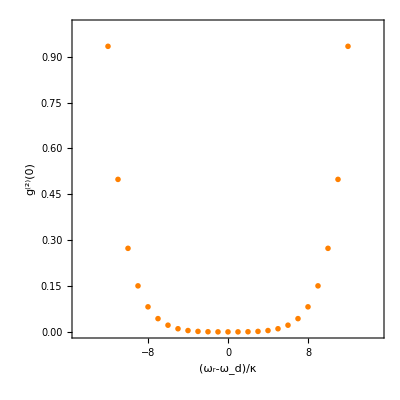

```mathematica
data={{-15.,1.029944151895725},{-14.,0.6055397447980336},{-13.,0.26608443876063154},{-11.999999999999998,-0.0296856384384351},{-10.999999999999998,-0.30211264525875287},{-10.,-0.5634409359571457},{-8.999999999999998,-0.82243350632647},{-7.999999999999999,-1.0864905532592775},{-7.,-1.362913798912641},{-6.,-1.6599462120985344},{-5.,-1.9879359450907292},{-4.,-2.360907224048729},{-2.9999999999999987,-2.798700519204637},{-1.9999999999999991,-3.3287939904087893},{-0.9999999999999996,-3.975892696331006},{0.,-4.480729421698302},{0.9999999999999996,-3.975892696331006},{1.9999999999999991,-3.3287939904087893},{2.9999999999999987,-2.798700519204637},{3.9999999999999982,-2.3609072240487303},{5.,-1.9879359450907292},{5.999999999999999,-1.6599462120985347},{6.999999999999999,-1.3629137989126408},{8.000000000000002,-1.086490553259276},{9.000000000000002,-0.8224335063264685},{10.000000000000002,-0.5634409359571448},{11.000000000000002,-0.30211264525875287},{12.,-0.0296856384384351},{13.,0.26608443876063154},{14.,0.6055397447980336},{15.,1.029944151895725}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Orange},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=64;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=38;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx,unity2];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz,unity2];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr,unity2];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl,unity2];
σx6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σx];
σz6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σz];
σr6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σr];
σl6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f+σl6f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f+σr6f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωq/2*σz6f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f))+g*(adaigef.adaigef.(σl5f)+af.af.(σr5f))+g*(adaigef.adaigef.(σl6f)+af.af.(σr6f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl6fcut=Take[SToH.σl6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr6fcut=Take[SToH.σr6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr6fcut,σl6fcut,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf)+γ/2*(2*σl6fcut.ρf.σr6fcut-ρf.σr6fcut.σl6fcut-σr6fcut.σl6fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,-15,15,1}];



data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

{{-15,0.882192},{-14,0.551768},{-13,0.251418},{-12,-0.0297086},{-11,-0.293862},{-10,-0.546218},{-9,-0.802589},{-8,-1.06368},{-7,-1.33802},{-6,-1.6278},{-5,-1.94835},{-4,-2.31167},{-3,-2.72244},{-2,-3.19898},{-1,-3.66544},{0,-3.87392},{1,-3.67179},{2,-3.19756},{3,-2.72266},{4,-2.31062},{5,-1.9489},{6,-1.62761},{7,-1.33748},{8,-1.06344},{9,-0.803768},{10,-0.54733},{11,-0.291358},{12,-0.0276342},{13,0.251285},{14,0.555322},{15,0.882918}}

```mathematica
data={{-15,0.8821922450969617},{-14,0.5517679657516381},{-13,0.25141773576490867},{-12,-0.029708623102677904},{-11,-0.2938618125364878},{-10,-0.5462181278790755},{-9,-0.8025891173323579},{-8,-1.0636795320224315},{-7,-1.3380170918982293},{-6,-1.6278036716668693},{-5,-1.9483463901498612},{-4,-2.3116743502645716},{-3,-2.7224429051059027},{-2,-3.1989836148103046},{-1,-3.6654417517442996},{0,-3.8739174174699977},{1,-3.6717864838121423},{2,-3.1975633190158885},{3,-2.7226615978906934},{4,-2.3106169541449186},{5,-1.948904759694161},{6,-1.6276070647108476},{7,-1.3374798432982236},{8,-1.063442675955195},{9,-0.8037682622679918},{10,-0.5473304080490292},{11,-0.2913584310098618},{12,-0.02763417905930311},{13,0.25128498244298464},{14,0.5553220013680648},{15,0.8829183197821671}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Orange},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

-Graphics-

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=7;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=15*κ;
min1=-15*κ;      (*max and min value of Δ*)
segment1=30;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=Sqrt[E1^2/(2 E1^2+4 Δ^2+κ^2)];

g=0.01*ωr;


equs=Table[{g*C2*Sqrt[2]+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*Sqrt[6]+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*Sqrt[2]*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*Sqrt[2]+E1/2*C3*Sqrt[3]-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*Sqrt[6]*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*Sqrt[3]-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/(E1^2/(2 E1^2+4 Δ^2+κ^2))^2];


{Δ/κ,logg20},{m,1,30+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{{-15.,0.556564},{-14.,0.247761},{-13.,-0.0252707},{-12.,-0.278288},{-11.,-0.521159},{-10.,-0.761053},{-9.,-1.00399},{-8.,-1.25575},{-7.,-1.52263},{-6.,-1.81223},{-5.,-2.13445},{-4.,-2.50301},{-3.,-2.93753},{-2.,-3.46534},{-1.,-4.11091},{0.,-4.61476},{1.,-4.11091},{2.,-3.46534},{3.,-2.93753},{4.,-2.50301},{5.,-2.13445},{6.,-1.81223},{7.,-1.52263},{8.,-1.25575},{9.,-1.00399},{10.,-0.761053},{11.,-0.521159},{12.,-0.278288},{13.,-0.0252707},{14.,0.247761},{15.,0.556564}}

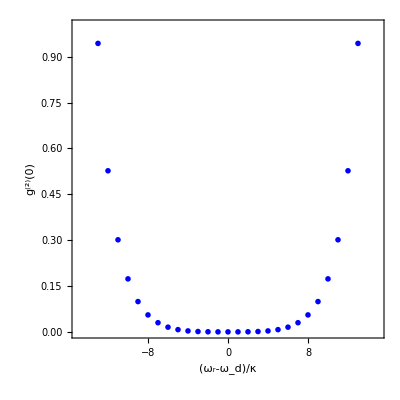

```mathematica
data={{-15.,0.5565639998694852},{-14.,0.2477606492127041},{-13.,-0.025270652956474182},{-11.999999999999998,-0.2782884140740346},{-10.999999999999998,-0.5211590075105067},{-10.,-0.7610532291572034},{-8.999999999999998,-1.003986343307596},{-7.999999999999999,-1.2557461508195589},{-7.,-1.5226301575359986},{-6.,-1.8122273167107732},{-5.,-2.134445492590174},{-4.,-2.5030051437447587},{-2.9999999999999987,-2.9375316413461343},{-1.9999999999999991,-3.465336031258325},{-0.9999999999999996,-4.1109087682930445},{0.,-4.614757024154298},{0.9999999999999996,-4.1109087682930445},{1.9999999999999991,-3.465336031258325},{2.9999999999999987,-2.9375316413461343},{3.9999999999999982,-2.5030051437447596},{5.,-2.134445492590174},{5.999999999999999,-1.8122273167107734},{6.999999999999999,-1.5226301575359982},{8.000000000000002,-1.2557461508195575},{9.000000000000002,-1.0039863433075942},{10.000000000000002,-0.7610532291572026},{11.000000000000002,-0.5211590075105067},{12.,-0.2782884140740346},{13.,-0.025270652956474182},{14.,0.2477606492127041},{15.,0.5565639998694852}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotMarkers->"OpenMarkers",PlotStyle->{Blue},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=128;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=47;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,Sqrt[2],0,0,0},{0,0,0,Sqrt[3],0,0},{0,0,0,0,2,0},{0,0,0,0,0,Sqrt[5]},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,Sqrt[2],0,0,0,0},{0,0,Sqrt[3],0,0,0},{0,0,0,2,0,0},{0,0,0,0,Sqrt[5],0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2,unity2,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2,unity2,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2,unity2,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2,unity2,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx,unity2,unity2];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz,unity2,unity2];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr,unity2,unity2];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl,unity2,unity2];
σx6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σx,unity2];
σz6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σz,unity2];
σr6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σr,unity2];
σl6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σl,unity2];
σx7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σx];
σz7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σz];
σr7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σr];
σl7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f+σl6f+σl7f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f+σr6f+σr7f;
Jxf=Jlf+Jrf;



(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=700;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωq/2*σz6f+ωq/2*σz7f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f))+g*(adaigef.adaigef.(σl5f)+af.af.(σr5f))+g*(adaigef.adaigef.(σl6f)+af.af.(σr6f))+g*(adaigef.adaigef.(σl7f)+af.af.(σr7f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl6fcut=Take[SToH.σl6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr6fcut=Take[SToH.σr6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl7fcut=Take[SToH.σl7f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr7fcut=Take[SToH.σr7f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr7fcut,σl7fcut,σr6fcut,σl6fcut,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf)+γ/2*(2*σl6fcut.ρf.σr6fcut-ρf.σr6fcut.σl6fcut-σr6fcut.σl6fcut.ρf)+γ/2*(2*σl7fcut.ρf.σr7fcut-ρf.σr7fcut.σl7fcut-σr7fcut.σl7fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,-15,15,1}];

data
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

{{-15,0.522813},{-14,0.239815},{-13,-0.020994},{-12,-0.267576},{-11,-0.505128},{-10,-0.741096},{-9,-0.979968},{-8,-1.22769},{-7,-1.49377},{-6,-1.77905},{-5,-2.0951},{-4,-2.45112},{-3,-2.86088},{-2,-3.33059},{-1,-3.79572},{0,-3.99816},{1,-3.80107},{2,-3.3322},{3,-2.86172},{4,-2.45168},{5,-2.09571},{6,-1.77752},{7,-1.49296},{8,-1.22839},{9,-0.98027},{10,-0.739418},{11,-0.503054},{12,-0.267205},{13,-0.0212097},{14,0.240362},{15,0.523515}}

```mathematica
data={{-15,0.5228134423168802},{-14,0.23981475506568087},{-13,-0.02099403705594326},{-12,-0.2675764131508136},{-11,-0.5051277199533585},{-10,-0.7410962151498991},{-9,-0.9799684257452318},{-8,-1.227688174089248},{-7,-1.4937720750163908},{-6,-1.7790512623407175},{-5,-2.0951042131837836},{-4,-2.451116800184454},{-3,-2.8608760000061575},{-2,-3.3305863718455844},{-1,-3.795721069193262},{0,-3.9981604113607285},{1,-3.8010675365437905},{2,-3.3321971192800675},{3,-2.8617247608717538},{4,-2.45168435155047},{5,-2.0957060305546977},{6,-1.7775219320668267},{7,-1.492959223447157},{8,-1.2283854406701082},{9,-0.9802695150353649},{10,-0.7394175084229364},{11,-0.5030537937271},{12,-0.2672049503313378},{13,-0.021209717856387433},{14,0.240361525629837},{15,0.5235153285081958}};
ListPlot[Table[{Chop[data[[i,1]]],10^data[[i,2]]},{i,1,31}],FrameLabel->{"(ω_r-ω_d)/κ","g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotMarkers->"*",PlotStyle->{Blue},Frame->True,PlotRange->{{-15,15},{0,1}},AspectRatio->1]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,BaseStyle->{FontSize->16,FontFamily->"Calibri"}]
```

-Graphics-